## Initialization

### Import dependencies

```mathematica
(* Run bubble-4a-murphree.nb before. *)
```

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}
```

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

```mathematica
If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

```mathematica
Get["MovingTrap-murphree.m"]
Get["FitCurveHacked-mean-murphree.m"]
```

The following variables used by ExpansionPlotHacked are protected by this package: {axis, trap, usemodel, frequency, trapposition, gridlines, size, meanfrequency, meanmodel}

### Define initial and final trap parameters

These values taken from SM3 “predictions”

```mathematica
(** Current to field magnitude conversion factors for Bias **)
BxCalib=40.625;(*[G/A]*)
ByCalib=14.286;(*[G/A]*)
BzCalib=-10.368;(*[G/A]*)

(** Max current values **)
(* Chip *)
IlbMax=3.5; (* [A] *)
IzbMax=-3.5;(* [A] *)
IhMax=5.;(* [A] *)

(* Bias coils *)
IbxMax=8.;(*[A]*)
IbyMax=3.02;(*[A]*)
IbzMax=3.;(*[A]*)

(** Table values **)
(* These were taken from CAL3A_chiptrap_v1.pdf *)
(* Initial trap *)
tableZLHb={
(* Chip *)
AZ1=0.243,(* % *)
AZ2=-0.686,(* % *)
H1pH2=0.46,(* % *) 

(* Bias coils *)
T1=0.0275,(*%*)
T2=T1,
Y=0.85,(*%*)
Z=-0.05(*%*)
};

fdec=0.2;
tableZLHbDecomp={
(* Chip *)
tableZLHb⟦1⟧, (* AZ1 [%] *)
tableZLHb⟦2⟧,(* AZ2 [%] *)
tableZLHb⟦3⟧,(* H1pH2 [%] *)

(* Bias coils *)
fdec*tableZLHb⟦4⟧,(* T1 [%] *)
fdec*tableZLHb⟦5⟧,(* T2 [%] *)
fdec*tableZLHb⟦6⟧,(* Y [%] *)
fdec*tableZLHb⟦7⟧(* Z [%] *)
};

tableZHb={
(* Chip *)
0., (* AZ1 [%] *)
-0.743, (* AZ2 [%] *)
0.46, (* H1pH2 [%] *)

(* Bias coils *)
-0.018, (* T1 [%] *)
-0.018, (* T2 [%] *)
0.63,(* Y [%] *)
-0.0001 (* Z [%] *)
};

tableZHbC={
(* Chip *)
0., (* AZ1 [%] *)
0.914, (* AZ2 [%] *)
0.26, (* H1pH2 [%] *)

(* Bias coils *)
-0.006125,(* T1 [%] *)
-0.006125,(* T2 [%] *)
0.0677, (* Y [%] *)
-0.11367 (* Z [%] *)
};

(* Trap CurrL, CurrZ, CurrH, Bx1, By1, Bz1 *)
defineTableFromTrap[trap_]:=Module[
{CurrL=trap⟦1⟧,
CurrZ=trap⟦2⟧,
CurrH=trap⟦3⟧,
Bx1=trap⟦4⟧,
By1=trap⟦5⟧,
Bz1=trap⟦6⟧,
table},

table={
CurrL/IlbMax, (*AZ1 [%]*)
CurrZ/IzbMax, (*AZ2 [%]*)
CurrH/IhMax, (*H1pH2 [%]*)

Bx1/(-1.*IbxMax*BxCalib), (*T1*)
Bx1/(-1.*IbxMax*BxCalib), (*T2*)
By1/(IbyMax*ByCalib), (*Y*)
Bz1/(IbzMax*BzCalib) (*Z*)
};
Return[table];
];

defineTrapFromTable[table_]:=Module[
{AZ1=table⟦1⟧,
AZ2=table⟦2⟧,
H1pH2=table⟦3⟧,
T1=table⟦4⟧,
T2=table⟦5⟧, (* Currently T2=T1, and so doesn't play role yet *)
Y=table⟦6⟧,
Z=table⟦7⟧,
trap},

trap={
(* Chip *)
AZ1*IlbMax,(*Ilb0 [A]*)
AZ2*IzbMax,(*Izb0 [A]*)
H1pH2*IhMax,(*Ih0 [A]*)

(* Bias coils *)
(-1.)*T1*IbxMax*BxCalib,(*Bx [G]*)
Y*IbyMax*ByCalib,(*By [G]*)
Z*IbzMax *BzCalib(*Bz [G]*)
};
Return[trap];
]

(* The Bates trap *)
currLa=0;
currZa=0;
currLb=0;
currZb=2.6;
currH = 2.6;

Bx1 = (-0.048)*40.625;
By1 = (0.43)*14.286;
Bz1 = (0.3003)*(-10.3675);

trapZHbB={currLa,currZa,currLb,currZb,currH,Bx1,By1,Bz1};
tableZHbB=convertTrapParametersToCALTable[trapZHbB,verbose->True];
(* *)

(* Package for resale: *)
(* Compare these values to those in SM3 "predictions", although Bzfinal, for us, should be multiplied by 0.2 *)
trapzero=defineTrapFromTable[tableZLHb]
trapone=trapZHbB⟦3;;⟧
(* Where the x turn happens. *)
trapone={0.11975890500000008,2.57197881,2.557757,-2.933909875000001,10.441794117420002,-2.4559802811975002}
(*trapone=trapzero⟦1;;3⟧~Join~trapone⟦4;;6⟧*)
(*trapone=defineTrapFromTable@defineTableFromTrap@{CurrL,CurrZ,CurrH,Bx1,By1,Bz1}*)
(*trapzero={0.11975890500000008,2.57197881,2.557757,-2.933909875000001,10.441794117420002,-2.4559802811975002}
trapone=trapZHbB⟦3;;7⟧~Join~{-3.1134}*)
```

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0,2.6,2.6,-1.95,6.14298,-3.11336}

{0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}

### Define target ramp analytic function

```mathematica
cass[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2 t^(1/4) -1)]/Tanh[5];
cassShort[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2(t/2)^(1/4) -1)]/Tanh[5];
```

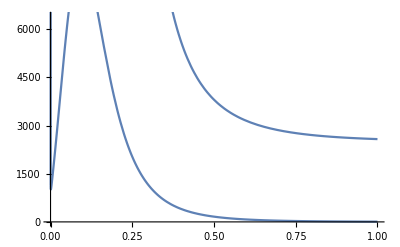

```mathematica
omegaPlot=Plot[cassShort[800,50,t]^2,{t,0,1},PlotRange->All];
dOmegaPlot=Plot[Evaluate[(1/0.5)*Abs@D[cassShort[800,50,t],t]],{t,0,1},PlotRange->All,PlotStyle->{"Red"}];
Show[omegaPlot,dOmegaPlot,PlotRange->{{0,1},{0,6400}}]
```

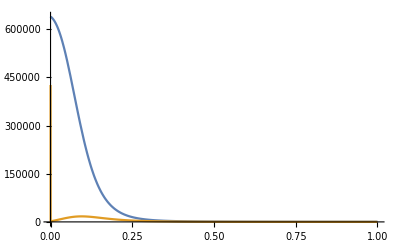

```mathematica
periodT=0.250 (* [s] *);
omegaI=800 (* [Hz] *);
omegaF=20 (* [Hz] *);
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->All,PlotStyle->{"Blue","Red"}]
```

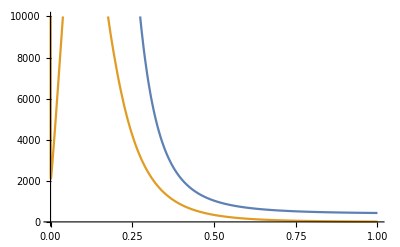

```mathematica
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->{{0,1},{0,1*10^4}},PlotStyle->{"Blue","Red"}]
```

21

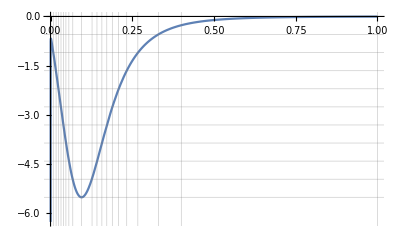

```mathematica
num=20;
times={0,0.0085,0.017,0.024,0.032,0.04,0.047,0.056,0.068,0.095,0.127,0.142,0.157,0.172,0.189,0.208,0.233,0.267,0.33,0.4,1};
Length@times
Plot[Evaluate[D[cassShort[1,0,t],{t,1}]],{t,0,1},GridLines->{times,Table[-k*max/(num/2),{k,1,num/2}]}]
```

```mathematica
Length@Differences@times
```

20

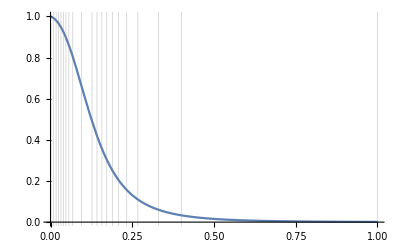

```mathematica
Plot[cassShort[1,0,t],{t,0,1},GridLines->{times,{}},PlotRange->Full]
```

```mathematica
max=MaxValue[{Abs@Evaluate[D[cassShort[1,0,t],{t,1}]],t>0.01},t]
```

5.51458

```mathematica
dCassShort[t_]=Evaluate[D[cassShort[1,0,t],{t,1}]];
```

```mathematica
(*InverseFunction@dCassShort*)
```

```mathematica
(*cassShortInv=InverseFunction@dCassShort*)
```

```mathematica
(*cassShortInv[-max]*)
```

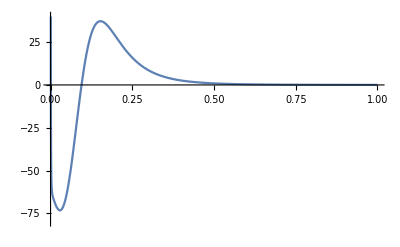

```mathematica
Plot[Evaluate[D[cassShort[1,0,t],{t,2}]],{t,0,1},PlotRange->{{0,1},{-80,40}}]
```

```mathematica
corgierSimp[t_]:=Module[{tau=2*Pi*t},
(1/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];
```

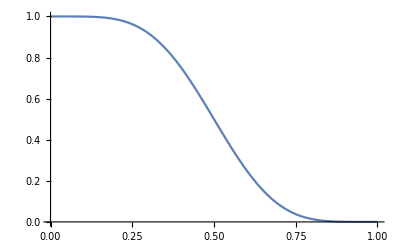

```mathematica
Plot[1-corgierSimp[t],{t,0,1}]
```

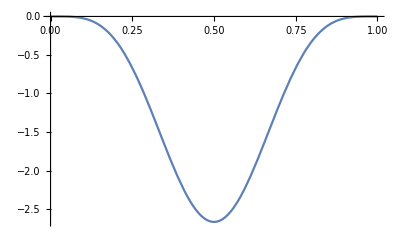

```mathematica
Plot[Evaluate@D[1-corgierSimp[t],t],{t,0,1}]
```

```mathematica
InverseFunction[corgierSimp][8/3]
```

Root2.56Root[{-32-(8 Sin[2 π #1])/π+Sin[4 π #1]/π+12 #1&,2.56420663113429131513147635321}]2.5642066311342915

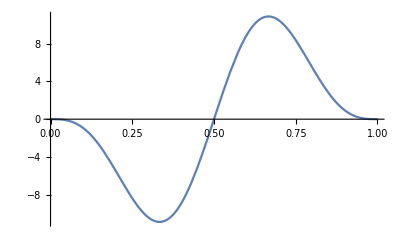

```mathematica
Plot[Evaluate@D[1-corgierSimp[t],{t,2}],{t,0,1}]
```

```mathematica
ArcCos[-1-2*Sqrt[2*6/10]]/(2*Pi)//N
```

0.5-0.290925 ⅈ

```mathematica
trapAnalytic[trap1_,trap2_,t_]:=trap1+(trap2-trap1)*(1-cassShort[1,0,t]);
zeroCrossing[trap1_,trap2_]:=(1/8)*((1/5)*ArcTanh[2*Tanh[5]*((1/2)-trap2[[6]]/(trap2[[6]]-trap1[[6]]))]+1)^4;
```

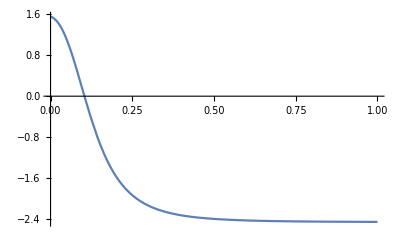

0.103674

tZero = 0.0518372

```mathematica
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All]
tauZero=zeroCrossing[trapzero,trapone]
period=500*10^(-3);
deltaTau=10*^-3/period;
newTaus={tauZero-deltaTau,tauZero,tauZero+deltaTau};
Print["tZero = "<>ToString[tauZero*period]]
```

```mathematica
Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,rampin1sguess⟦1⟧}]
```

{{0.85,-2.44761},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676}}

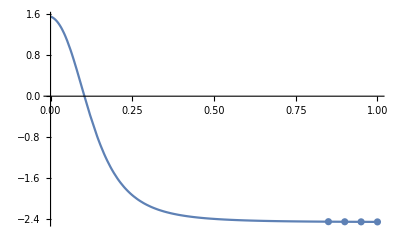

```mathematica
Show[{
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All],
ListPlot[Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,Accumulate@rampin1sguess⟦1⟧}]]
}]
```

### Define ramp ansatz

#### Trap 1 Short

```mathematica
rampin1sguess={{0.02,0.02,0.02,0.014,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.036,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.014,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.036,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
rampin1sguess={2*{0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.025,0.04,0.07,0.08,0.09},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
(* Successful ramp with sharp tail "20200908T174440_trap1short.csv" *)
rampin1sguess={{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.15},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.02982,0.00749}}
```

{{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.15},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.02982,0.00749}}

```mathematica
(* Ignoring population guesses, since they don't factor into the fitting. *)
rampin1sguess={{0.85,0.05, 0.05, 0.05},{0.85,0.05, 0.05, 0.05}}
```

{{0.85,0.05,0.05,0.05},{0.85,0.05,0.05,0.05}}

```mathematica
(*(* New as of 4 September 2020---an attempt to divy up the ramp based on its slope *)
Total@Differences@times
rampin1sguess={Differences@times,{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}*)
```

```mathematica
Table[Total@#[[1,1;;m]],{m,Length@#[[1]]}]&[rampin1sguess]
```

{0.85,0.9,0.95,1.}

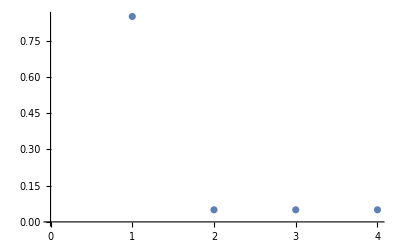

```mathematica
ListPlot[rampin1sguess⟦2⟧]
```

```mathematica
(*rampin1sguess⟦1,9;;13⟧
rampin1sguess⟦1⟧=Join[rampin1sguess⟦1,1;;9⟧,{0.01,0.01,0.01,0.01,0.01},rampin1sguess⟦1,10;;⟧]
rampin1sguess⟦1,9;;18⟧
rampin1sguess⟦1,9;;18⟧={0.02,0.02,0.02,0.01,0.01,0.01,0.01,0.01,0.02,0.02}*)
```

```mathematica
(*rampin1sguess⟦2,9;;13⟧
rampin1sguess⟦2⟧=Join[rampin1sguess⟦2,1;;9⟧,ConstantArray[0.,5],rampin1sguess⟦2,10;;⟧]*)
```

```mathematica
(*rampin1sguess*)
```

```mathematica
Total[rampin1sguess⟦1⟧]
```

1.

```mathematica
Total[rampin1sguess⟦2⟧]
```

1.

```mathematica
Length@rampin1sguess[[1]]
```

4

## Calculate ramp

The following took 8 1/2 minutes to complete. (1 1/4 hr on the Dell)

```mathematica
(* 
If FitCurveHacked runs in less than a second and has multiple errors citing GeometricMean, go back and make sure bubble-4a.nb was run before this notebook. MovingTrap-murphree.m calls ChipTrapFrequencies, which is defined in that notebook.
*)
```

```mathematica
nramps1short=Length@rampin1sguess⟦1⟧
(rampin1s=FitCurveHacked[trapzero,trapone,rampin1sguess,nramps1short,-3.5,-5,"CorgierSin"])//Timing
```

4

{0.85,40.1561,0.00001,76.0866,1.,0}

{0.925,18.4591,0.00001,76.0866,1.,0.85}

{0.9625,8.59093,0.00001,76.0866,1.,0.925}

{0.98125,3.89034,0.00001,76.0866,1.,0.9625}

{0.99062,1.59757,0.00001,76.0866,1.,0.98125}

{0.99531,0.463752,0.00001,76.0866,1.,0.99062}

{0.99765,-0.0985402,0.00001,76.0866,1.,0.99531}

{0.99648,0.182323,0.00001,76.0866,0.99765,0.99531}

{0.99706,0.0430214,0.00001,76.0866,0.99765,0.99648}

{0.99735,-0.0265777,0.00001,76.0866,0.99765,0.99706}

Completed point 1 of 3 in 68.9063 s (Total time: 1.14844 min).

{0.000933333,1.00365,0.00001,74.8686,0.0028,0}

{0.00187,0.779388,0.00001,74.8686,0.0028,0.000933333}

{0.00233,0.669385,0.00001,74.8686,0.0028,0.00187}

{0.00256,0.614417,0.00001,74.8686,0.0028,0.00233}

{0.00268,0.585746,0.00001,74.8686,0.0028,0.00256}

{0.00274,0.571413,0.00001,74.8686,0.0028,0.00268}

{0.00277,0.564247,0.00001,74.8686,0.0028,0.00274}

{0.00278,0.561858,0.00001,74.8686,0.0028,0.00277}

{0.00279,0.55947,0.00001,74.8686,0.0028,0.00278}

{0.00279,0.55947,0.00001,74.8686,0.0028,0.00279}

{0.00279,0.55947,0.00001,74.8686,0.0028,0.00279}

{0.00279,0.55947,0.00001,74.8686,0.0028,0.00279}

«7 more identical outputs»

$Aborted

```mathematica
rampin1s⟦2⟧-rampin1sguess⟦2⟧
```

{-0.01951,-0.04045,-0.06094,-0.07344,-0.07183,-0.05535,-0.07096,-0.02677,0.01662,0.05082,0.0717,0.08114,0.08024,0.06853,0.04882,0.01927,-0.01313,-0.00476}

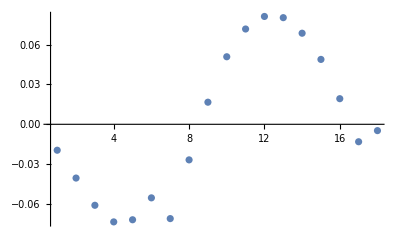

```mathematica
ListPlot[%,PlotRange->All]
```

The following took ~4 1/2 minutes to run. (~ 1 hr 12 min on Dell)

```mathematica
points1s=100;
(pts1s=MovingTrap[trapzero,trapone,rampin1s,points1s,nramps1short];)//Timing
```

{400.578,Null}

```mathematica
Position[pts1s⟦All,1,1⟧,Min@pts1s⟦All,1,1⟧]
```

{{86}}

```mathematica
pts1s⟦31⟧
```

{{0.0000714595,-0.0000209735,0.000144324},{111.038,895.343,860.221},8.69537}

```mathematica
Length@pts1s
```

101

```mathematica
trapParamVt=RampList[trapzero,trapone,rampin1s,points1s,nramps1short];
```

```mathematica
trapParamVt[[31]]
```

{0.3,{0.797156,2.41348,2.31882,-8.49924,34.7573,1.26238}}

### Plot calculated ramp’s parameters

{{0.,1.},{4.69813,6.83513}}

{109.742,929.95}

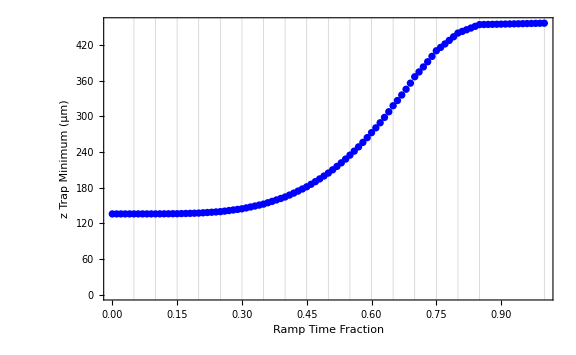
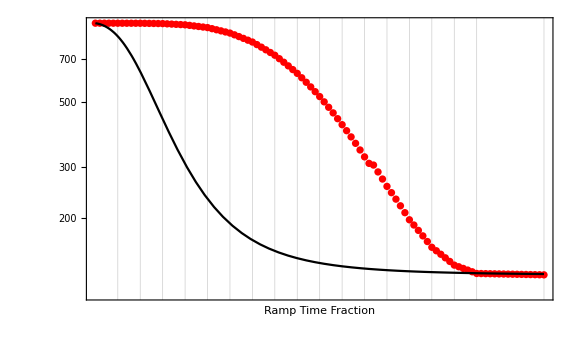

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"z"]
```

{{0.,1.},{3.19789,4.77009}}

{24.4807,117.929}

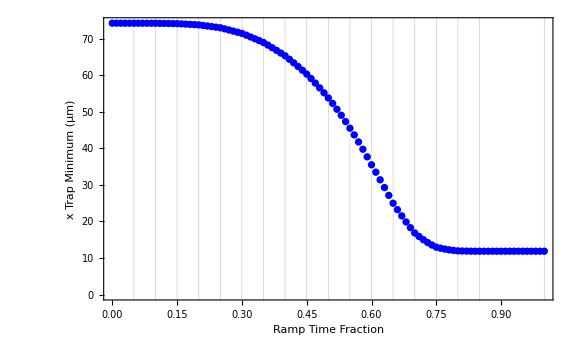
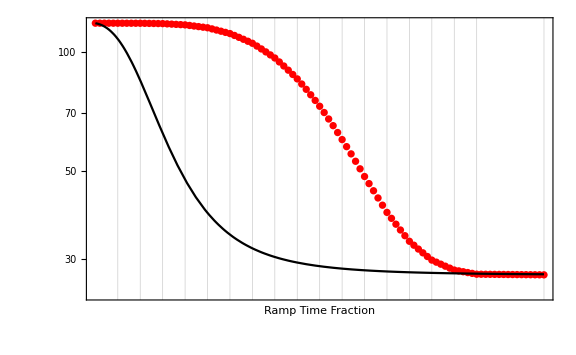

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"x",meanfrequency->False]
```

{{0.,1.},{4.6421,6.87598}}

{103.762,968.724}

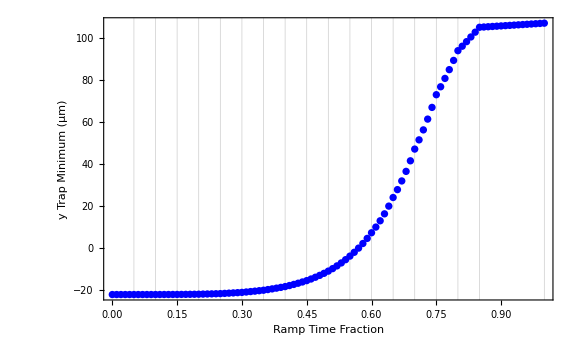
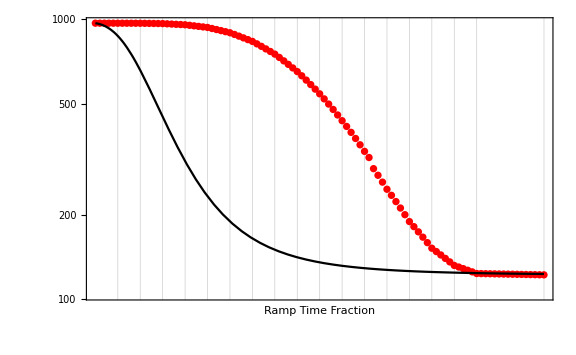

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"y",meanfrequency->False]
```

{{0.,1.},{4.69813,6.83513}}

{109.742,929.95}

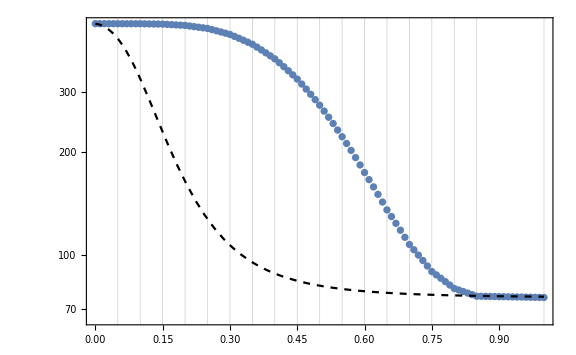

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->False,frequency->False,gridlines->True,usemodel->True,size->Large,axis->"z",meanfrequency->True,meanmodel->True]
```

```mathematica
Beep[]
```

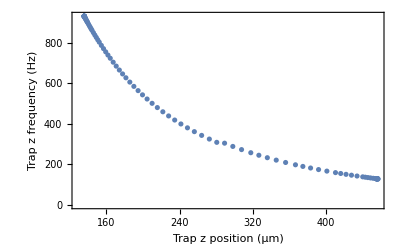

```mathematica
plotZFreqVZmin[movingtrap_]:=Module[{zs,omegas},
zs[n_]:=movingtrap⟦n,1,3⟧*10^6;
omegas[n_]:=movingtrap⟦n,2,3⟧;

ListPlot[Table[{zs[n],omegas[n]},{n,Range[Length[movingtrap]]}],Frame->True,FrameLabel->{"Trap z position (μm)","Trap z frequency (Hz)"}]
]
plotZFreqVZmin[pts1s]
```

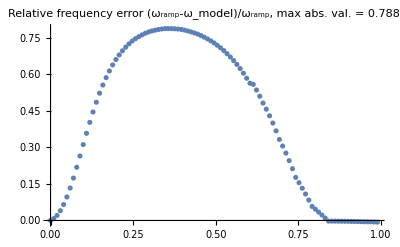

```mathematica
plotFreqError[pts1s]
```

```mathematica
printTrapParameters[{{minx_,miny_,minz_},{omegax_,omegay_,omegaz_},bmin_}]:=Print[
"Position = "<>ToString[{minx,miny,minz}*10^6]<>" μm\n"<>
"Frequency = "<>ToString[{omegax,omegay,omegaz}]<>" Hz\n"<>
"Bmin = "<>ToString[bmin]<>" G"];

printTrapParameters[pts1s⟦1⟧]
printTrapParameters[pts1s⟦-1⟧]
```

Position = {74.2507, -21.9915, 135.717} μm
Frequency = {117.929, 968.724, 929.95} Hz
Bmin = 8.97843 G

Position = {11.8576, 106.845, 456.854} μm
Frequency = {27.4397, 122.025, 128.153} Hz
Bmin = 5.60963 G

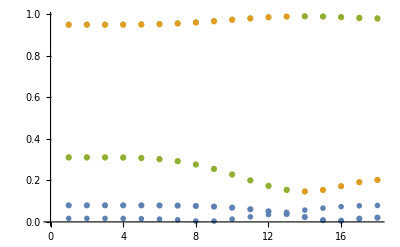

```mathematica
plotTrapPrincAxes[trap1_,trap2_,rampin_]:=Module[
{nramps=Length@rampin⟦1⟧,
eVecIndex,
characVtime,
vec2Plot,vec3Plot},
characVtime=Table[SingleTrapCharacteristics[trap1,trap2,rampin,nramps,n],{n,nramps}];
eVecIndex=2;
vec2Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}],PlotMarkers->"OpenMarkers"];
eVecIndex=3;
vec3Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}]];
Show[vec2Plot,vec3Plot]
]
plotTrapPrincAxes[trapzero,trapone,rampin1s]
```

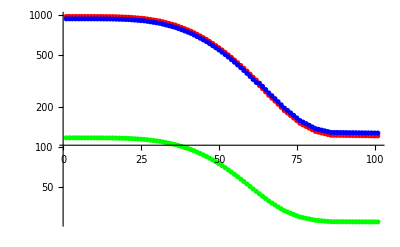

```mathematica
plotTrapYandZCharacteristics[movingramp_]:=Module[
{xFreqs=movingramp⟦All,2,1⟧,
yFreqs=movingramp⟦All,2,2⟧,
zFreqs=movingramp⟦All,2,3⟧,
xPlot,yPlot,zPlot},
xPlot=ListLogPlot[xFreqs,PlotStyle->Green];
yPlot=ListLogPlot[yFreqs,PlotStyle->Red];
zPlot=ListLogPlot[zFreqs,PlotStyle->Blue];
Show[yPlot,zPlot,xPlot,PlotRange->All]
]
plotTrapYandZCharacteristics[pts1s]
```

## Export ramp

### Export ramp

```mathematica
trap1short={#⟦1⟧,Table[Total[Take[Round[#⟦2⟧,10.^-5],n]],{n,Length@rampin1s⟦1⟧}]}&[rampin1s]
```

{{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.15},{0.00031,0.00064,0.00327,0.01248,0.03329,0.073,0.13465,0.21888,0.32316,0.44029,0.56242,0.68119,0.78927,0.87866,0.94292,0.98058,0.99727,1.}}

```mathematica
(* Set the DateStringFormat to help create unique names for each exported beam.The format is inspired by the ISO 8601 standard. *)
generateTimeStamp[]:=DateString[{"Year","Month","Day","T","Hour","Minute","Second"}];
rampTimeStamp=generateTimeStamp[]
```

20200908T174440

```mathematica
Export[FileNameJoin@{outputDirectory,rampTimeStamp<>"_trap1short.csv"},trap1shortᵀ]
```

C:\Users\josep\forschung\modeling\bubble_bec\output\20200908T174440_trap1short.csv

### Export ramp parameters

```mathematica
exportRampEndpoints[trap1_,trap2_,rampTimeStamp_,outputDirectory_]:=Module[
{
fileName=rampTimeStamp<>"_ramp_endpoints",
table={trap1,trap2},
headings={{"InitialTrap","FinalTrap"},{"IL[A]","IZ[A]","IH[A]","Bx[G]","By[G]","Bz[G]"}}
},
Print[table];
Export[FileNameJoin@{outputDirectory,fileName<>".csv"},table,TableHeadings->headings]
]

exportRampEndpoints[trapzero,trapone,rampTimeStamp,outputDirectory]
```

{{0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}}

C:\Users\josep\forschung\modeling\bubble_bec\output\20200908T174440_ramp_endpoints.csv

```mathematica
Beep[];
Pause[1];
Beep[];
```

```mathematica
defineTableFromTrap[trapone]
```

{0.0342168,-0.734851,0.511551,0.00902742,0.00902742,0.242024,0.0789603}

## Look at intermediate trap and CAL table values

{{0., 0.8505}, {0.01, 0.850455}, {0.02, 0.850409}, {0.03, 0.850364}, {0.04, 0.850319}, {0.05, 0.850273}, {0.06, 0.850225}, {0.07, 0.850177}, {0.08, 0.850129}, {0.09, 0.850081}, {0.1, 0.850032}, {0.11, 0.849648}, {0.12, 0.849264}, {0.13, 0.848879}, {0.14, 0.848495}, {0.15, 0.84811}, {0.16, 0.846764}, {0.17, 0.845418}, {0.18, 0.844072}, {0.19, 0.842726}, {0.2, 0.84138}, {0.21, 0.838339}, {0.22, 0.835298}, {0.23, 0.832256}, {0.24, 0.829215}, {0.25, 0.826174}, {0.26, 0.82037}, {0.27, 0.814567}, {0.28, 0.808763}, {0.29, 0.802959}, {0.3, 0.797156}, {0.31, 0.788146}, {0.32, 0.779136}, {0.33, 0.770126}, {0.34, 0.761116}, {0.35, 0.752106}, {0.36, 0.739796}, {0.37, 0.727486}, {0.38, 0.715176}, {0.39, 0.702865}, {0.4, 0.690555}, {0.41, 0.675315}, {0.42, 0.660075}, {0.43, 0.644834}, {0.44, 0.629594}, {0.45, 0.614354}, {0.46, 0.597235}, {0.47, 0.580117}, {0.48, 0.562999}, {0.49, 0.54588}, {0.5, 0.528762}, {0.51, 0.510913}, {0.52, 0.493064}, {0.53, 0.475215}, {0.54, 0.457366}, {0.55, 0.439517}, {0.56, 0.422159}, {0.57, 0.404801}, {0.58, 0.387443}, {0.59, 0.370084}, {0.6, 0.352726}, {0.61, 0.336931}, {0.62, 0.321135}, {0.63, 0.305339}, {0.64, 0.289544}, {0.65, 0.273748}, {0.66, 0.260684}, {0.67, 0.24762}, {0.68, 0.234555}, {0.69, 0.221491}, {0.7, 0.208427}, {0.71, 0.199036}, {0.72, 0.189644}, {0.73, 0.180253}, {0.74, 0.170861}, {0.75, 0.16147}, {0.76, 0.155966}, {0.77, 0.150462}, {0.78, 0.144958}, {0.79, 0.139454}, {0.8, 0.13395}, {0.81, 0.131511}, {0.82, 0.129071}, {0.83, 0.126632}, {0.84, 0.124193}, {0.85, 0.121754}, {0.86, 0.121621}, {0.87, 0.121488}, {0.88, 0.121355}, {0.89, 0.121222}, {0.9, 0.121089}, {0.91, 0.120956}, {0.92, 0.120823}, {0.93, 0.12069}, {0.94, 0.120557}, {0.95, 0.120424}, {0.96, 0.120291}, {0.97, 0.120158}, {0.98, 0.120025}, {0.99, 0.119892}, {1., 0.119759}}

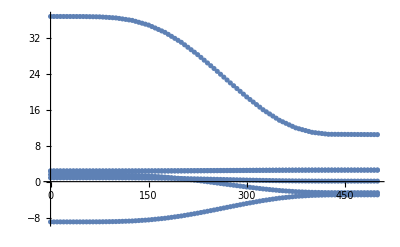

```mathematica
listRampCALTables[trap1_,trap2_,rampin_,npoints_,nramps_:3]:=Module[
{
deltatrap=trap1-trap2,
ramp=Prepend[Table[{Sum[#[[1,i]],{i,n}],Sum[#[[2,i]],{i,n}],#[[2,n]]/#[[1,n]]},{n,nramps}]&[rampin],{0,0,0}],
ramplist,
colors={"Red","Orange","Yellow","Green","Blue","Black"}
},

ramplist=Prepend[Drop[Table[{t,Piecewise[Table[{#3-(#1[[n-1,2]]+#1[[n,3]]*(t-#1[[n-1,1]]))*#2,#1[[n-1,1]]<t<=#1[[n,1]]},{n,2,nramps+1}]&[ramp,deltatrap,trap1]]},{t,0.,1.,1./npoints}],1],{0.,trap1}];

Print[ToString[{#[[1]],#[[2,1]]}&/@ramplist]];

Return[Table[ListPlot[{#⟦1⟧*500,#⟦2,k⟧}&/@ramplist,PlotStyle->colors⟦k⟧],{k,6}]];
];
test=listRampCALTables[trapzero,trapone,rampin1s,points1s,nramps1short];
Show[test,PlotRange->All]
```

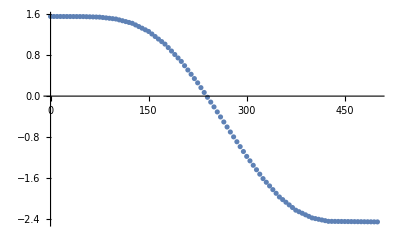

```mathematica
test[[6]]
```

```mathematica
rampin1s
```

{{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.15},{0.00031,0.00033,0.00263,0.00921,0.02081,0.03971,0.06165,0.08423,0.10428,0.11713,0.12213,0.11877,0.10808,0.08939,0.06426,0.03766,0.01669,0.00273}}

```mathematica
plotRampCALTable[trap1_,trap2_,rampin_]:=Module[
{
deltaTrap=trap2-trap1,
totRamp=Table[{Total@rampin⟦1,1;;k⟧,Total@rampin⟦2,1;;k⟧},{k,Length@rampin⟦1⟧}]~Prepend~{0,0},
trapRamp
},
trapRamp=Table[(totRamp⟦k,2⟧*deltaTrap+trap1)~Prepend~totRamp⟦k,1⟧,{k,Length@rampin⟦1⟧+1}];
Return[trapRamp];
];
trapRamp=plotRampCALTable[trapzero,trapone,rampin1s]
trapzero
trapone
```

{{0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.05,0.850273,2.40105,2.30008,-8.93564,36.664,1.55396},{0.1,0.850032,2.40111,2.30016,-8.93366,36.6554,1.55263},{0.15,0.84811,2.40156,2.30084,-8.91787,36.5864,1.54208},{0.2,0.84138,2.40313,2.30322,-8.86258,36.3448,1.50514},{0.25,0.826174,2.40669,2.30858,-8.73764,35.799,1.42167},{0.3,0.797156,2.41348,2.31882,-8.49924,34.7573,1.26238},{0.35,0.752106,2.42402,2.33471,-8.12912,33.1402,1.01509},{0.4,0.690555,2.43842,2.35642,-7.62343,30.9309,0.677233},{0.45,0.614354,2.45625,2.3833,-6.99738,28.1956,0.258947},{0.5,0.528762,2.47628,2.41349,-6.29418,25.1232,-0.210883},{0.55,0.439517,2.49716,2.44497,-5.56096,21.9197,-0.700768},{0.6,0.352726,2.51747,2.47558,-4.84791,18.8043,-1.17718},{0.65,0.273748,2.53595,2.50344,-4.19905,15.9693,-1.6107},{0.7,0.208427,2.55123,2.52648,-3.66239,13.6246,-1.96926},{0.75,0.16147,2.56222,2.54304,-3.27659,11.939,-2.22702},{0.8,0.13395,2.56866,2.55275,-3.0505,10.9512,-2.37808},{0.85,0.121754,2.57151,2.55705,-2.9503,10.5134,-2.44503},{1.,0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}}

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}

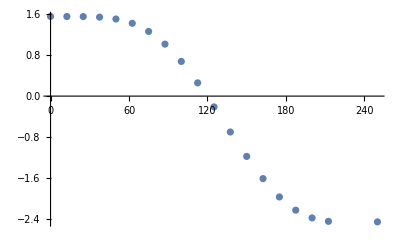

```mathematica
ListPlot[{#[[1]]*250,#[[7]]}&/@trapRamp]
```

```mathematica
Total@{1,2,3,4,5}
```

15